```mathematica
AppendTo[$Path,NotebookDirectory[] <> "../src/"];
<<affine.m;
```

```mathematica
fun[ls_:{0,1}]:=Module[{},Plus@@ls]
```

```mathematica
fun[{1,2,3}]
```

6

```mathematica
minimalCharacters[{ls1__Integer},ls2_:{0,1}]:=
Module[{
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]],ch1,ch2,wgs,res,pmults,subs,rh},
a1a[gradeLimit]=5;
ch1=character[makeIrreducibleModule[a1a][ls1]];
ch2=character[makeIrreducibleModule[a1a]@@ls2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
{conformalWeight[weight[a1a][ls1]]+conformalWeight[weight[a1a]@@ls2]-conformalWeight[#],Affine`Private`stringSelector[res,#,8]}&/@Select[res[weights],grade[#]==0&]]
```

```mathematica
minimalCharacters[{0,1}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+3 q^6+3 q^7+5 q^8},{1/2,1+q+q^2+q^3+2 q^4+2 q^5+3 q^6+4 q^7+5 q^8}}

```mathematica
minimalCharacters[{0,1},{1,0}]
```

{{1/16,1+q+q^2+2 q^3+2 q^4+3 q^5+4 q^6+5 q^7+6 q^8}}

```mathematica
minimalCharacters[{1,0},{1,0}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+3 q^6+3 q^7+5 q^8}}

```mathematica
minimalCharacters[{0,2}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+4 q^6+4 q^7+7 q^8},{3/5,1+q+2 q^2+2 q^3+4 q^4+5 q^5+7 q^6+9 q^7+13 q^8}}

```mathematica
minimalCharacters[{1,1}]
```

{{3/80,1+q+2 q^2+3 q^3+4 q^4+6 q^5+8 q^6+11 q^7+15 q^8},{7/16,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+10 q^8}}

```mathematica
minimalCharacters[{2,0}]
```

{{1/10,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8}}

```mathematica
minimalCharacters[{2,0},{1,0}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+4 q^6+4 q^7+7 q^8}}

```mathematica
minimalCharacters[{1,1},{1,0}]
```

{{3/80,1+q+2 q^2+3 q^3+4 q^4+6 q^5+8 q^6+11 q^7+15 q^8}}

```mathematica
minimalCharacters[{2,0},{1,0}]
```

{{1/10,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8},{1/2,q+q^2+2 q^3+2 q^4+3 q^5+4 q^6+6 q^7+7 q^8}}

```mathematica
minimalCharacters[{3,0}]
```

{{1/8,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8}}

```mathematica
minimalCharacters[{2,1}]
```

$Aborted

```mathematica
minimalCharacters[{1,2}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5+9 q^6+12 q^7+17 q^8},{21/40,1+q+2 q^2+3 q^3+5 q^4+7 q^5+10 q^6+14 q^7+19 q^8}}

```mathematica
minimalCharacters[{0,3},{1,0}]
```

{{5/8,q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+9 q^7+12 q^8},{1/8,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8}}

```mathematica
minimalCharacters[{2,1},{1,0}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5+9 q^6+12 q^7+17 q^8}}

```mathematica
minimalCharacters[{0,3}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5},{2/3,1+q+2 q^2+2 q^3+4 q^4+5 q^5},{1,q^2+q^3+2 q^4+3 q^5}}

```mathematica
minimalCharacters[{2,1}]
```

{{1/15,1+q+2 q^2+3 q^3+5 q^4+7 q^5},{2/5,1+q+q^2+2 q^3+3 q^4+4 q^5}}

```mathematica
minimalCharacters[{1,2}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5},{21/40,1+q+2 q^2+3 q^3+5 q^4+7 q^5}}

```mathematica
minimalCharacters[{3,0},{1,0}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5}}

```mathematica
minimalCharacters[{2,1},{1,0}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5}}

```mathematica
minimalCharacters[{1,2},{1,0}]
```

{{1/15,1+q+2 q^2+3 q^3+5 q^4+7 q^5},{2/5,q+q^2+2 q^3+2 q^4+4 q^5}}

```mathematica
minimalCharacters[{0,3},{1,0}]
```

{{1/8,1+q+q^2+2 q^3+3 q^4+4 q^5},{5/8,q+q^2+2 q^3+3 q^4+4 q^5}}

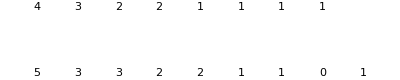

```mathematica
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]];
a1a[gradeLimit]=8;
mod1=makeIrreducibleModule[a1a][1,0];
mod2=makeIrreducibleModule[a1a][1,0];
ch1=character[mod1];
ch2=character[mod2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
affinePlot[res]
```

```mathematica
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]];
a1a[gradeLimit]=8;
mod1=makeIrreducibleModule[a1a][0,1];
mod2=makeIrreducibleModule[a1a][1,0];
ch1=character[mod1];
ch2=character[mod2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
affinePlot[res]
```

-Graphics-

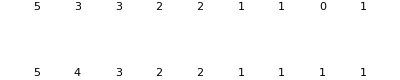

```mathematica
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]];
a1a[gradeLimit]=8;
mod1=makeIrreducibleModule[a1a][0,1];
mod2=makeIrreducibleModule[a1a][0,1];
ch1=character[mod1];
ch2=character[mod2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
affinePlot[res]
```

```mathematica
affinePlot[f_formalElement,opts___?OptionQ]:=
Graphics[(Text[f[#],{grade[#],#[finitePart][standardBase][[1]]}]&)/@f[weights],opts]
```

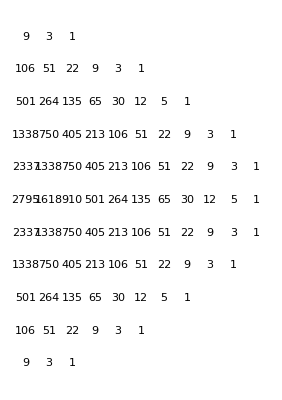

```mathematica
affinePlot[pmults]
```

```mathematica
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
```

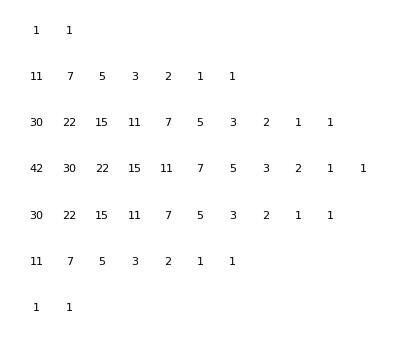

```mathematica
affinePlot[ch1]
```

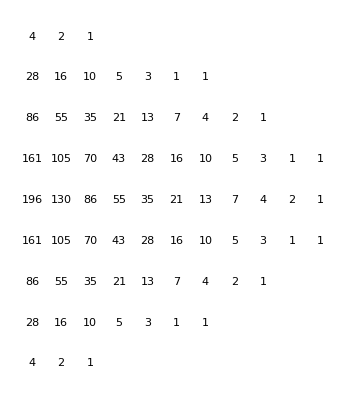

```mathematica
affinePlot[ch2]
```

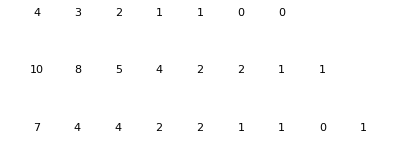

```mathematica
affinePlot[res]
```

```mathematica
rho[a1a]
```

affineWeight[1,finiteWeight[1,{1/(√2)}],2,0]

```mathematica
conformalWeight[hw1_]:=hw1.(hw1+2*rho[a1a])/(2*(level[hw1]+2))
```

```mathematica
conformalWeight[weight[a1a][1,0]]+conformalWeight[weight[a1a][0,1]]-conformalWeight[weight[a1a][2,0]]
```

1/4

```mathematica
ch3=ch1*ch2
```

$Aborted

```mathematica
c1=character[makeIrreducibleModule[Subscript[A, 1]][2]];
c2=character[makeIrreducibleModule[Subscript[A, 1]][3]];
```

```mathematica
(c1*c2)[multiplicities]
```

{1,2,3,3,2,1}

```mathematica
c3=makeFormalElement@@Transpose[Flatten[Outer[{#1+#2,c1[#1]*c2[#2]}&,c1[weights],c2[weights]],1]]
```

formalElement[Affine`Private`table$1533]

```mathematica
c3[multiplicities]
```

{1,3,2,3,1,2}